```mathematica
Clear[f]
```

```mathematica
F0'[r_]:=f''[r]*r^2+4*f'[r]*r+2*f[r]-2
```

```mathematica
F0[r_]:=∫(-2+2 f[r]+4 r f'[r]+r^2 f''[r])ⅆr
```

```mathematica
F1[r_]:=3*f'[r]*r^2+4*f[r]*r
```

```mathematica
F2[r_]=2*f[r]*r^2
```

2 r^2 f[r]

```mathematica
D[(2 r^2 f[r]), r]
```

4 r f[r]+2 r^2 f'[r]

```mathematica
Simplify[Solve[F0[r]-F1[r]+F2'[r]==-μ,f[r]]]
```

{{f[r]→1-μ/(2 r)}}

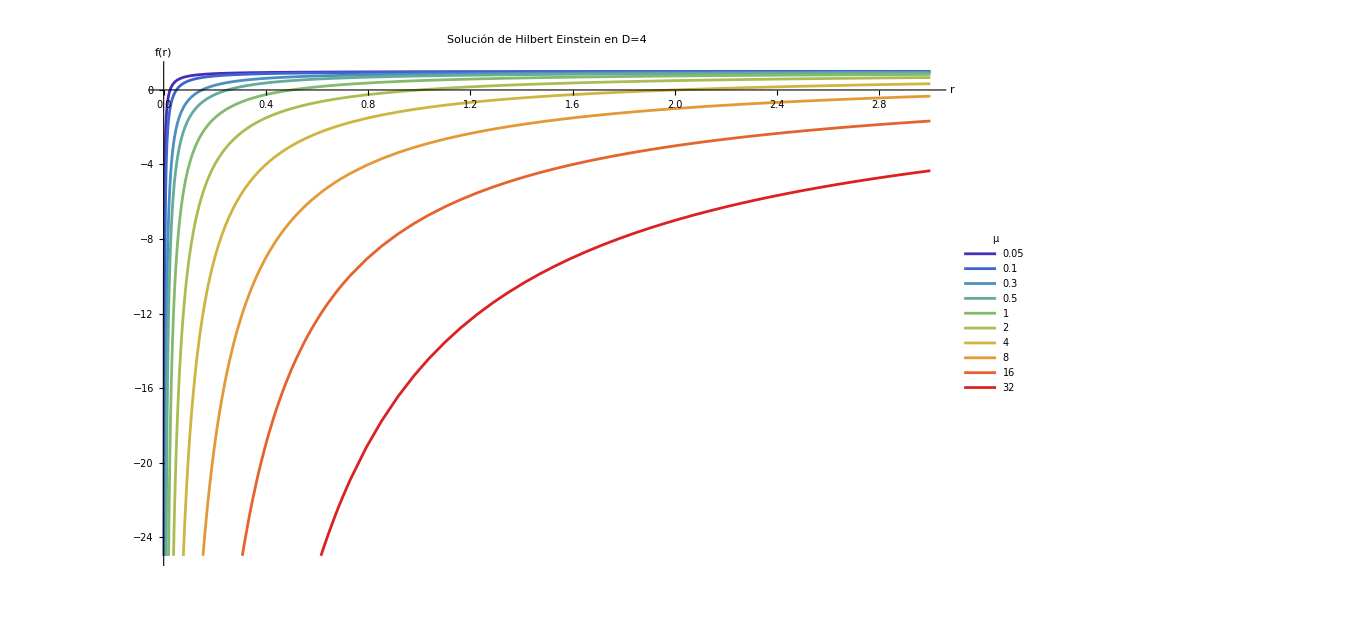

```mathematica
valoresMu:={0.05,0.1,0.3,0.5,1,2,4,8,16,32};fig3=Plot[Evaluate@Table[1-μ/(2 r),{μ,valoresMu}],{r,0,3},PlotRange->{1,-25},PlotStyle->Table[ColorData["Rainbow"][i/Length[valoresMu]],{i,Length[valoresMu]}],PlotLegends->Placed[LineLegend[valoresMu,LegendLabel->Style["μ",18,Bold]],{0.8,0.35}],AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold]},PlotLabel->Style["Solución de Hilbert Einstein en D=4",20,Bold],ImageSize->{1000,600}]
```

```mathematica
Export["Hilbert-Einstein 4D.png",fig3]
```

Hilbert-Einstein 4D.png